```mathematica
iterate[polygon_List]:=If[DuplicateFreeQ@Differences@polygon,
With[{n=Length@polygon},
{t=If[n~Divisible~4,Cot,Csc],c=2^-Mod[n,2]},
{r=c t[c π/n]+1},Plus@##/r&],(#1+2#2)/3&];
(*--------------------------------------------------------------*)
pointset[polygon_List,scale_:1,n_:10^6]:=With[{f=iterate[polygon]},
{r=CoordinateBounds@polygon,list=RandomChoice[N@polygon,n]},
FoldList[f,scale RandomReal/@r,list]];
(*--------------------------------------------------------------*)
frames[polygon_List,steps_]:=Module[{f=iterate[polygon],
choice,list,r=Range[Length@polygon],
points,mark,text,route,walk},
list=polygon[[choice=r~RandomChoice~steps]];
points=FoldList[f,RandomReal/@CoordinateBounds[polygon],list];
mark={PointSize@Medium,Red,Point[#]}&/@points;
text=Text[Style[#,Orange,FontSize->36],Mean@polygon]&/@choice;
route=MapThread[{Blue,Dashed,Line@{##}}&,{Most@points,list}];
walk=MapThread[{LightMagenta,Line@{##}}&,#[points]&/@{Most,Rest}];
list=Thread[{Most@mark,text,route,walk}]~Flatten~1;
Graphics/@{
GraphicsComplex[polygon,Point@r],
ListPlot[Labeled[polygon[[#]],Text[#],Bottom]&/@r,PlotStyle->Green],
Sequence@@list,Last@mark}];
(*--------------------------------------------------------------*)
index[n_Integer] :=Take[{1,3,2},UpTo@n]~Join~SortBy[
Select[Range[4,n],#>=4Quotient[n+2,4]||#~Mod~4>1&],
Mod[#,2]&];
```

```mathematica
coeff(n_Integer):=With[{t=If[4∣#1,Cot,Csc]&,c=2^-n2},c t(n)((π c)/n)+1];
rInverse(n_Integer):=2(1+ ∑_(k=1)^Floor[n/4] cos((2 π k)/n));
Chop@N@Table[coeff(i)-rInverse(i),{i,20}]
```

{-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
triangle={{0,1},{-1,-1},{1.5,-1}};
```

```mathematica
With[{a=frames[triangle,15]},
With[{f=Show[a[[index@#]],ImageSize->Large]&/@Range[Length@a]},
Export["walksteps.gif",f,"DisplayDurations"->.5]]];
Directory[]
```

```mathematica
With[{steps=Import["https://i.stack.imgur.com/KRiRX.gif"]},
Animate[Show[steps[[n]],ImageSize->Large],{n,1,Length@steps,1},
AnimationRunning->False,AnimationRate->.7]]
```

```mathematica
With[{a=frames[triangle,50]},
Animate[Show[a[[index@n]],ImageSize->Large],{n,2,Length@a,1},
AnimationRunning->False,AnimationRate->.7]]
```

#### Implementation of the Chaos Game

```mathematica
set=pointset[triangle];
```

```mathematica
game[steps_Integer] := Module[{p1, p2, p3,size},
size=(1+15Log[#,#/steps]^1.35)&[Length@set]/2.1;
p1={PointSize[Large],Darker@Green,Point[triangle]};
p2=Text[Style["steps" steps,Blue,FontSize->20],{1.2,.9}];
p3={AbsolutePointSize@size,Red,Point@set[[1;;steps]]};
Show[Graphics/@{p1, p2, p3},ImageSize->Large]]
```

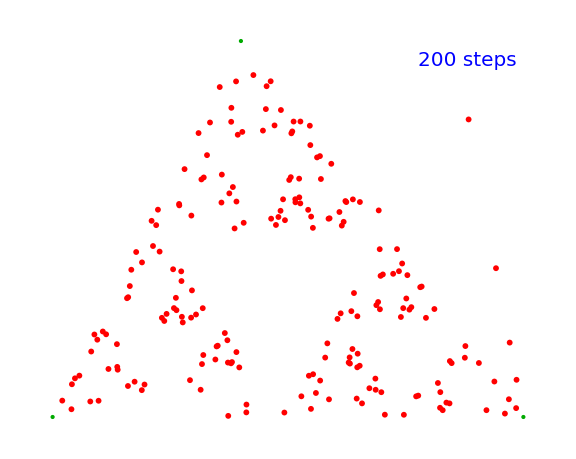

```mathematica
game[200]
```

```mathematica
Manipulate[game@Round[1.304^n],{n,2,52,1}]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-{2,1}]},
With[{frames=game@Round[#]&/@p},
Export["game.gif",frames,"DisplayDurations"->.4]]];
```

#### Sierpiński carpet

```mathematica
set=pointset@Most@Tuples[{-1,1,0},2];
```

```mathematica
carpet[n_Integer]:= Module[{ p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@set]/2.1;
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@set[[1;;n]]};
Show[Graphics/@{p1, p2},PlotRange->1.05, ImageSize -> Large]]
```

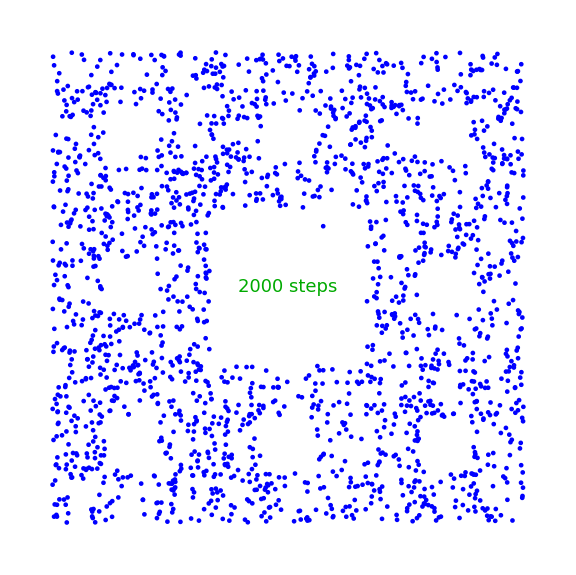

```mathematica
carpet[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-Range[9,1,-1]]},
With[{frames=carpet@Round[#]&/@p},
Export["carpet.gif",frames,"DisplayDurations"->.4]]];
```

#### Pentagonal Snowflake

```mathematica
set=pointset@CirclePoints[5];
```

```mathematica
flake5[n_Integer]:= Module[{r, p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@set]/2.1;
r=CoordinateBounds@CirclePoints[5]/GoldenRatio;
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@set[[1;;n]]};
Show[Graphics[#,PlotRange->1.05r]&/@{p1, p2},ImageSize -> Large]]
```

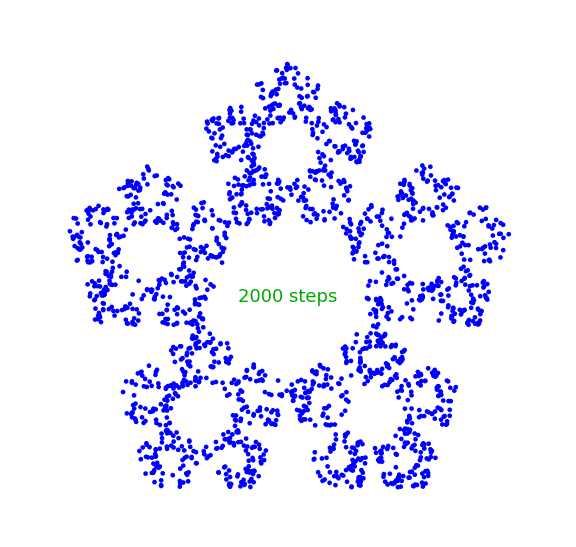

```mathematica
flake5[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-{2,1}]},
With[{frames=flake5@Round[#]&/@p},
Export["flake5.gif",frames,"DisplayDurations"->.4]]];
```

#### Hexagonal Snowflake

```mathematica
set=pointset@CirclePoints[6];
```

```mathematica
flake6[n_Integer]:= Module[{r, p1, p2,size},
size=(1+15Log[#,#/n]^1.13)&[Length@set]/2.1;
r=CoordinateBounds@CirclePoints[6]/2;
p1=Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
p2={AbsolutePointSize@size,Blue,Point@set[[1;;n]]};
Show[Graphics[#,PlotRange->1.05r]&/@{p1, p2},ImageSize -> Large]]
```

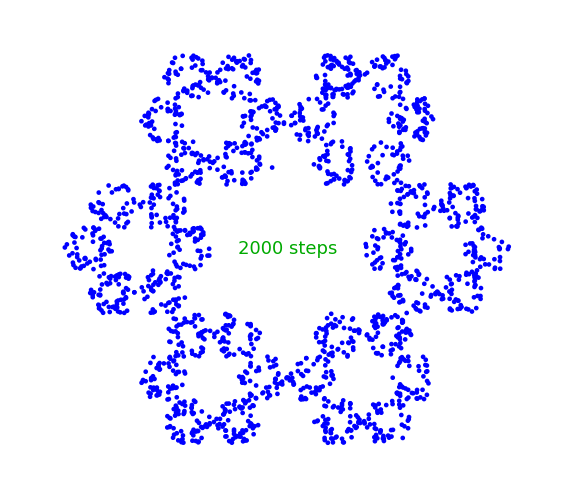

```mathematica
flake6[2000]
```

```mathematica
With[{p=Join[1.304^Range[2,52],Length@set-{2,1}]},
With[{frames=flake6@Round[#]&/@p},
Export["flake6.gif",frames,"DisplayDurations"->.4]]];
```

#### Fractal generation

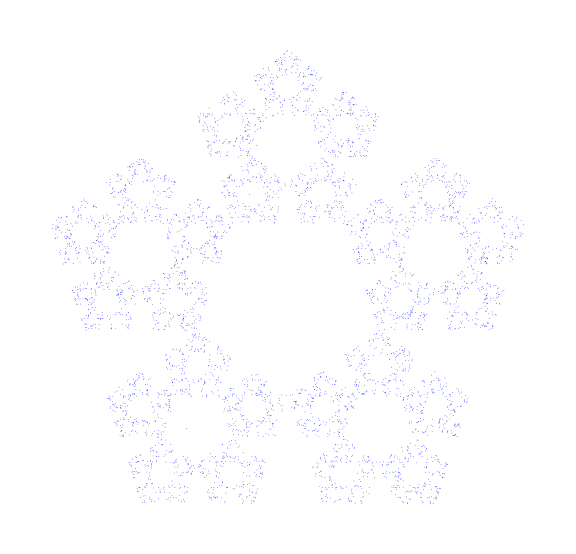

```mathematica
set=pointset[CirclePoints[5],1/2];
Graphics[{AbsolutePointSize[1/2],Blue,Point@set[[1;;5000]]},ImageSize -> Large]
```

```mathematica
Do[set=pointset[CirclePoints[n],0];
Export["fractal"<>ToString[n]<>".png",
Show[Graphics@{AbsolutePointSize[1/2],Blue,Point@set},ImageSize -> 2000]],{n,3,11}];
```

```mathematica
t=ConstantArray[Graphics[],9];
Do[set=pointset[CirclePoints[n+2],0];
t[[n]]=Show[Graphics/@{{AbsolutePointSize[1/2],Blue,Point@set},
Text[Style[n+2, Darker@Green,FontSize -> 120],{0,0}]},ImageSize -> 2000],{n,9}];
Export["table.png",Grid@Partition[t,3]];
```